```mathematica
Lecture 9: Single Variable Calculus
```

Key calculus functions include:

```mathematica
{Limit,D,Integrate,NIntegrate,FindRoot,Solve,Series,Normal,Maximize,NMaximize,Evaluate,ArcLength}
```

## Limits

### Exercise Subsection

Use known Calculus theorems and definitions to predict the output of the following cells:

```mathematica
Clear[f,x,a,c]
Limit[(f[x+h]-f[x])/h,h->0,Analytic->True]
```

f'[x]

```mathematica
Limit[(f[x]-f[a])/(x-a),x->a,Analytic->True]
```

f'[a]

```mathematica
Limit[c f[x],x->a,Analytic->True]==c Limit[f[x],x->a,Analytic->True]
```

True

### Exercise Subsection

A sequence a[n]where n is a positive integer is defined in the next cell.

```mathematica
a[n_]:=n! ⅇ^n n^(-n-1/2)
```

Create a graphic that shows the ListPlot to plot the first 1000 values of this sequence along with a line depicting its limit at Infinity.

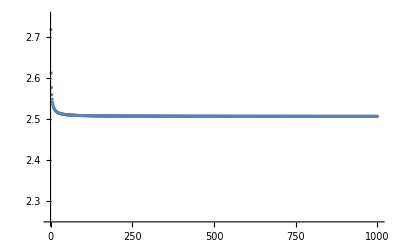

```mathematica
G1=ListPlot[a@Range@1000,PlotRange->{2.25,2.75}]
```

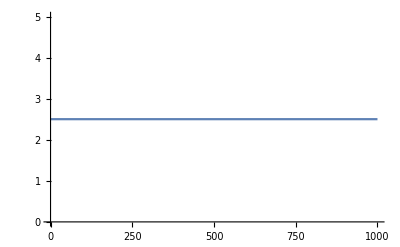

```mathematica
G2=Plot[Sqrt[2 Pi],{x,0,1000}]
```

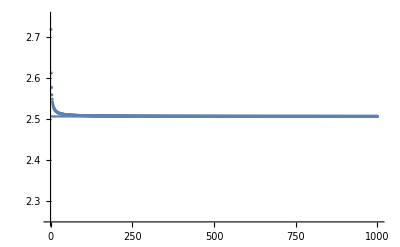

```mathematica
Show[G1,G2]
```

```mathematica
Limit[a[n],n->Infinity]
```

√(2 π)

### Exercise Subsection

Plot the function defined in the next cell and then create a graphic showing the plot of the function together with its limit at Infinity.

```mathematica
f[x_]:=(ⅇ^x x+Sin[x]+Cos[x] Sinh[x])/(ⅇ^x x+Sin[x])
```

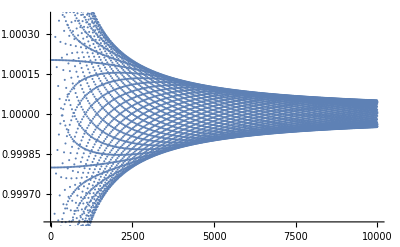

```mathematica
ListPlot@f@Range@10000
```

### Exercise Subsection

a. Produce a graphic that shows the ParametricPlot of the circle described by the parametric equations {Cos[t],Sin[t]} together with the inscribed polygon created by connecting 12 equally spaced points on the circle.

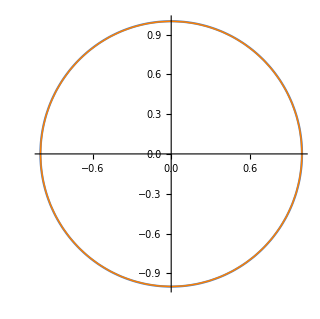

```mathematica
G1=ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}];
G2=Graphics[{Orange,Line@Table[{Cos[t],Sin[t]},{t,0,2Pi,2Pi/64}]}];
Show[G1,G2]
```

b. Use ArcLength to find the arc length of the inscribed polygon, thereby approximating the value of 2 Pi.

```mathematica
2 Pi-ArcLength@Line@Table[{Cos[t],Sin[t]},{t,0,2Pi,2 Pi/64}]//N
```

0.00252299

## Derivatives

### Exercise Subsection

Plot the function Cos[x] and the tangent line to Cos[x] at x = Pi/6.

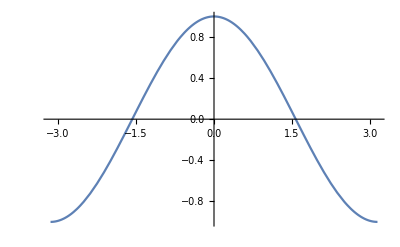

```mathematica
G1=Plot[Cos[x],{x,-Pi,Pi}]
```

```mathematica
D[Cos[x],x]/.{x->Pi/6}
```

-1/2

```mathematica
y=m x + b/.{m->-1/2}
```

b-x/2

```mathematica
Solve[(b-x/2)/.{x->Pi/6}==Cos[Pi/6],b]
```

ReplaceAll::reps: {{x→π/6}==(√3)/2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {(x→π/6)==(√3)/2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::naqs: b-x/2/.(x→π/6)==(√3)/2 is not a quantified system of equations and inequalities.

Solve[b-x/2/.{x→π/6}==(√3)/2,b]

```mathematica
Solve[Evaluate[(b-x/2)/.{x->Pi/6}]==Cos[Pi/6],b]
```

{{b→1/12 (6 √3+π)}}

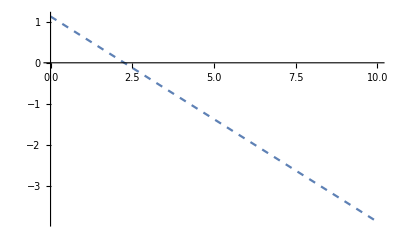

```mathematica
G2=Plot[Evaluate[m x + b/.{m->-1/2,b->1/12 (6 √3+π)}],{x,0,10},PlotStyle->Dashed]
```

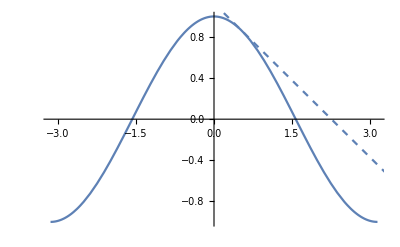

```mathematica
Show[G1,G2]
```

### Exercise Subsection

Find the maximum value of the function x^(a/x) where both x and a are positive.

```mathematica
Solve[D[x^(a/x),x]==0,x]
```

{{x→ⅇ}}

### Exercise Subsection

The mean value theorem says that if f[x] is differentiable for values of x between a and b, then there a point c strictly between a and b such that f’[c]=(f[b]-f[a])/(b-a).

a. Let f[x] be the function defined in the next cell.  Find one such value of c in the mean value theorem (consider selecting one of the the real elements of NSolve that is in the correct interval) when taking a to be the number that minimizes f[x] (consider Minimize) and b is the number that maximizes f[x] (consider Maximize).

```mathematica
f[x_]:=(x+1)/(2+x^2)
```

```mathematica
Minimize[f[x],x]
```

{-(√3)/(2+(-1-√3)^2),{x→-1-√3}}

```mathematica
a=x/.Last@Minimize[f[x],x]
b=x/.Last@Maximize[f[x],x]
```

-1-√3

-1+√3

```mathematica
c=First@Cases[c/.Solve[f'[c]==(f[b]-f[a])/(b-a),c]//Simplify,d_/;Im@d==0&&a<d<b]//N
```

-1.20035

b. Plot the following on the same graphic to illustrate the geometric meaning of the mean value theorem. 
1. The Plot of f[x] on the interval from a to b.
2. A Point at each of {a,f[a]}, {b,f[b]}, {c,f[c]}.
3. The InfiniteLine passing through the points {a,f[a]} and {b,f[b]}.
4. The InfiniteLine tangent to f[x] at x=c.

```mathematica
G1=Plot[f[x],{x,a,b}];
```

```mathematica
G2=Graphics[{Red,PointSize->.025,Point[{a,f[a]}],Point[{b,f[b]}],Point[{c,f[c]}],Orange,InfiniteLine[{{a,f[a]},{b,f[b]}}],Darker@Darker@Purple,InfiniteLine[{c,f[c]},{1,f'[c]}]}];
```

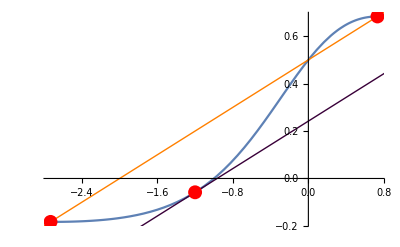

```mathematica
Show[G1,G2]
```

```mathematica
Animate[Show[G1,Graphics[{Red,InfiniteLine[{c,f[c]},{1,f'[c]}]}]],{c,a,b}]
```

## Integrals

### Exercise Subsection

Use known Calculus theorems and definitions to predict the output of the following cells:

```mathematica
Clear[f]
```

```mathematica
D[∫_a^t f[x]ⅆx,t]
```

f[t]

```mathematica
∫D[f[x],x]ⅆx
```

f[x]

### Exercise Subsection

Let f[x_,σ_,μ_] be the function defined in the next cell:

```mathematica
f[x_,σ_,μ_]:=1/(σ √(2 π))Exp[-(x-μ)^2/(2 σ^2)]
```

a. Use Manipulate to Plot the function f as a function of x where σ can take values between 1/4 and 4 and μ values between -4 and 4. Be sure to set PlotRange and any other Plot options to best illustrate the situation.

```mathematica
Manipulate[Plot[f[x,σ,μ],{x,-5,5},PlotRange->{-1,4}],{σ,1/4,4},{μ,-4,4}]
```

b. Find all critical points (where the derivative is equal to 0) and all inflection points (where the second derivative is 0) for f as a function of x.  Consider using Reduce as an alternative to Solve.

```mathematica
Solve[D[f[x,σ,μ],x]==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→μ}}

```mathematica
Solve[D[f[x,σ,μ],{x,2}]==0,x]
```

{{x→μ-σ},{x→μ+σ}}

c. Simplify the Integral of f with respect to x on the interval from 0 to ∞, both without any assumptions and then with the Simplify assumptions of And[Element[σ,Reals],σ >0,μ==0].

```mathematica
Simplify[Integrate[f[x,σ,μ],{x,0,∞}],And[Element[σ,Reals],σ >0,μ==0]]
```

1/2

### Exercise Subsection

The this integral is from the final round of the 2023 MIT integration bee:

```mathematica
Integrate[Tan[x]^(1/3)/(Cos[x]+Sin[x])^2,x]
```

ArcTan[(-1+2 Tan[x]^(1/3))/(√3)]/(√3)+1/3 Log[1+Tan[x]^(1/3)]-1/6 Log[1-Tan[x]^(1/3)+Tan[x]^(2/3)]+(-1+Sin[x]/(Cos[x]+Sin[x])) Tan[x]^(1/3)

Evaluate the integral and then use FunctionSingularities to describe the values of x for which the resulting function is not defined (where the function has a division by 0 singularity).

```mathematica
FunctionSingularities[ArcTan[(-1+2 Tan[x]^(1/3))/(√3)]/(√3)+1/3 Log[1+Tan[x]^(1/3)]-1/6 Log[1-Tan[x]^(1/3)+Tan[x]^(2/3)]+(-1+Sin[x]/(Cos[x]+Sin[x])) Tan[x]^(1/3),x]
```

Cos[x]==0||Cos[x]+Sin[x]==0||Tan[x]^(1/3)≤-1||-Tan[x]^(1/3)+Tan[x]^(2/3)≤-1||Tan[x]≤0

### Exercise Subsection

The average value of a function f[x] on the interval from a to b is given by Integrate[f[x],{x,a,b}]/(b-a).  Find a value of t such that the average value of the function Exp[-x] Sin[x] on the interval from 0 to t is equal to 1 (consider FindRoot).

### Exercise Subsection

The probabilist's Hermite polynomials are a sequence of polynomials defined by the recursion H[0,x] is equal to 1 and H[n,x] is equal to x H[n-1,x] - D[H[n-1,x],x] otherwise.

a. What is the 50th Hermite polynomial?  (Use Expand in the definition of the recursion together with memoization to get better results.)

b. Create a 8x8 matrix with i,j entry equal to ∫_(-∞)^∞ 1/(√(2 π))Exp[-x^2/2]*H[i,x]*H[j,x]ⅆx and then make a conjecture about what the entries of the corresponding nxn matrix would be.

```mathematica
Clear[H]
```

```mathematica
H[0,x_]:=1
H[n_Integer/;n>0,x_]:=H[n,x]=Expand[x H[n-1,x]-D[H[n-1,x],x]]
```

```mathematica
H[10,x]
```

-945+4725 x^2-3150 x^4+630 x^6-45 x^8+x^10

```mathematica
Table[Integrate[Exp[-x^2/2]H[i,x]H[j,x]/Sqrt[2 Pi],{x,-Infinity,Infinity}],{i,8},{j,8}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 6 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 24 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 120 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 720 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 5040 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 40320)

```mathematica
Integrate[Exp[-x^2/2]H[12,x]H[12,x]/Sqrt[2 Pi],{x,-Infinity,Infinity}]==12!
```

True

## Series

### Exercise Subsection

Show that the first 100 terms in the series for Exp[I x] is equal to the first 100 terms in the series for Cos[x] + I Sin[x].

```mathematica
Normal@Series[Exp[I x],{x,0,10}]==Normal@Series[Cos[x]+I Sin[x],{x,0,10}]
```

True

### Exercise Subsection

a. Use ListAnimate to show the Plot of of the function 1/(1-x) on the interval from -4 to 4 together with the degree n polynomial Series[1/(1-x),{x,0,n}] as n ranges from 0 to 25.

b. Redo part a. two more times, once when taking -1 as the center of the series instead of 0, and once when taking 1/2 as the center of the series.

```mathematica
ListAnimate@Table[Plot[{1/(1-x),Evaluate@Normal@Series[1/(1-x),{x,4,n}]},{x,-5,5},PlotRange->{-5,5},AspectRatio->1],{n,0,25}]
```

### Exercise Subsection

Use SumConvergence to determine the values of x for which this sum converges:

```mathematica
∑_(n=0)^∞ Log[Log[n]]^-x/(n Log[n])
```

```mathematica
?SumConvergence
```

```mathematica
SumConvergence[Log[Log[n]]^-x/(n Log[n]),n]
```

x>1

```mathematica
∑_(n=2)^(10^6) Log[Log[n]]^-2/(n Log[n])//N
```

43.3958

### Exercise Subsection

A twin prime is a prime p such that either p-2 or p+2 is also prime.  It is known that the sum of terms of the form 1/p where p is a twin prime converges.  Approximate this sum by selecting the twin primes from the first 10^6 primes and summing the reciprocals.

```mathematica
Apply[Plus,1/Cases[Prime@Range[10^7],p_/;PrimeQ[p-2]||PrimeQ[p+2]]]//N
```

1.56322